```mathematica
(* only works up to some amount because of noinfo; seems to up to 28 *) 
With[{monWin=#}, With[{infoIntPointList = tallyInfoInTriplesets[generateSuccessOutcomeWithTripleset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)monWin, (* attempts per each subset size *)2, interWald, 0.95, oneIntervalTestRetPair], "h1count",monFilenames, (*monwin again*)monWin]}, 
With[{interChart =  ListPlot[{#[[1]], #[[2,1]]}&/@infoIntPointList, PlotRange->Full],  
estChart = ListPlot[{#[[1]], #[[2,2]]}&/@infoIntPointList, PlotStyle->{Lighter@Purple, PointSize[Medium]}], gtChart = chartHorLine[predFNR[0.1, monWin], Max@infoIntPointList[[All,1]]]},
Show[interChart, estChart , gtChart]]
]]&/@ Range[2, 30]
```

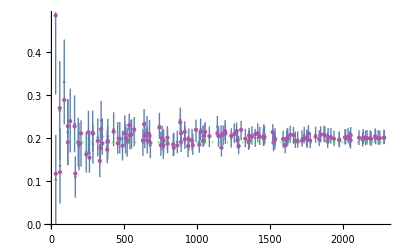
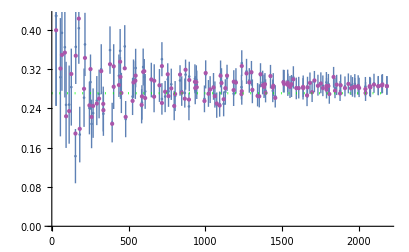
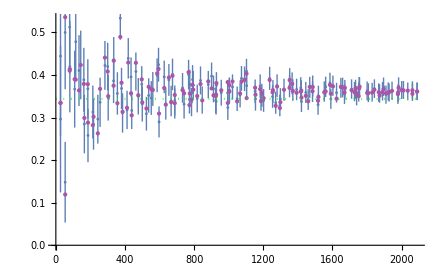
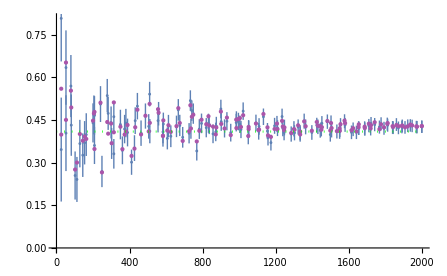
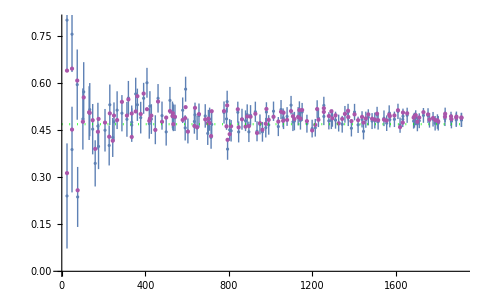
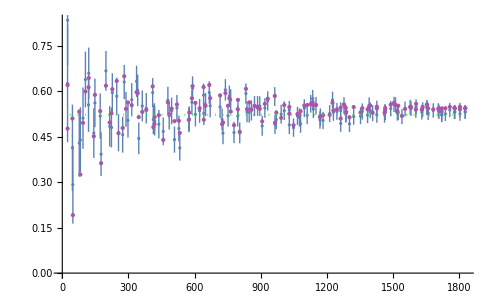
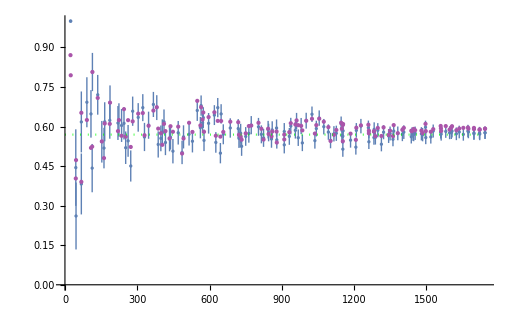
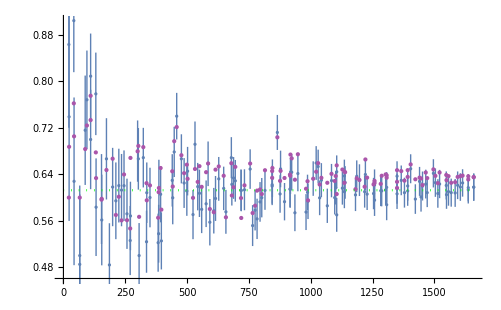
```mathematica
2 -Graphics-,
3 -Graphics-,
4-Graphics-,
5-Graphics-,
6-Graphics-,
7-Graphics-,
8-Graphics-,
9-Graphics-,
10 -Graphics-,
11 -Graphics-,
12 -Graphics-,
13-Graphics-,
14-Graphics-,
15-Graphics-,
16 -Graphics-,
17-Graphics-,
18-Graphics-,
19-Graphics-,
20-Graphics-,
21 -Graphics-,
22 -Graphics-,
23-Graphics-,
24-Graphics-,
25-Graphics-,
26 -Graphics-,
27-Graphics-,
28-Graphics-,29 -Graphics-
```

```mathematica
(*** NICE PRESENTATION-READY VISUALS ***) 
intEstGtChart = With[{monWin=10}, With[{infoIntPointList = tallyInfoInTriplesets[generateSuccessOutcomeWithTripleset[pairingPredMonFNR,fullTripleListNoRedun, {4,5,6,7}, (*monwin size*)monWin, (* attempts per each subset size *)2, interWald, 0.95, oneIntervalTestRetPair], "h1count",monFilenames, (*monwin again*)monWin]}, 
With[{interChart =  ListPlot[{#[[1]], #[[2,1]]}&/@infoIntPointList,PlotStyle->{Darker@Blue}, PlotRange->Automatic],  
estChart = ListPlot[{#[[1]], #[[2,2]]}&/@infoIntPointList, PlotStyle->{Darker@Magenta, PointSize[Large]}], gtChart = chartHorLine[predFNR[0.1, monWin], Max@infoIntPointList[[All,1]]]},
Show[interChart, estChart , gtChart]]
]]
```

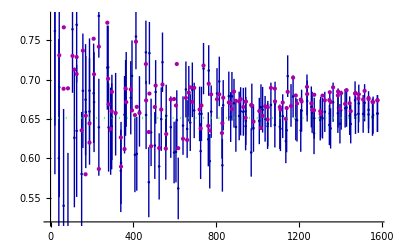
```mathematica
intEstGtChart5 = -Graphics-;
```

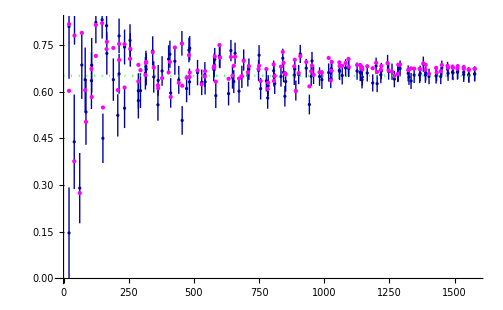
```mathematica
intEstGtChart4=-Graphics-;
```

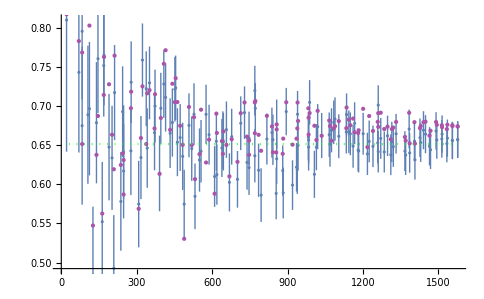
```mathematica
intEstGtChart3 = -Graphics-;
```

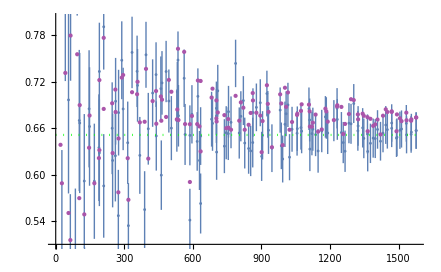
```mathematica
intEstGtChart2=-Graphics-;
```

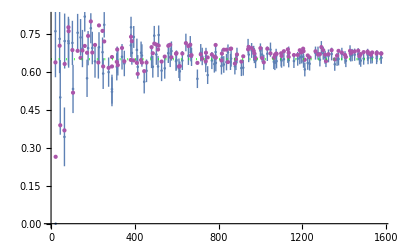
```mathematica
intEstGtChart1 = -Graphics-;
```

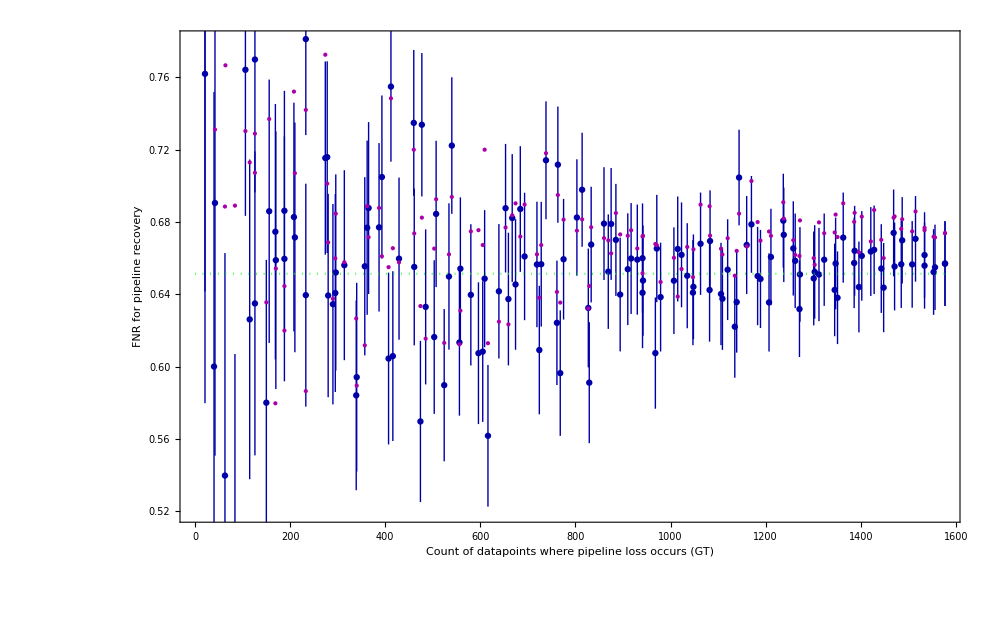

```mathematica
Show[intEstGtChart5,Frame->True, FrameLabel->{Style["Count of datapoints where pipeline loss occurs (GT)", 14],Style["FNR for pipeline recovery", 14]},   ImageSize -> 1000]
```

```mathematica
Export["~/graph.png",%737, ImageSize->1000] ;
```

```mathematica
SwatchLegend[{ Darker@Blue,Darker@Magenta, Green},{"Confidence interval for data-based FNR estimate","Our prediction of FNR","Absolute error of our FNR estimate","Ground-truth FNR"}, LegendMarkers->{ "|",●, —}]
```

```mathematica
Export["~/graph.png",%741, ImageSize->1000] ;
```